```mathematica
(*$LoadAddOns={"FeynHelpers"};*)
```

```mathematica
<< FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
SetOptions[A0,A0ToB0->True]
```

{A0ToB0→True}

```mathematica
(*Install["/home/marcela/Desktop/Dropbox/LoopTools-2.14/x86_64-Linux/bin/LoopTools"]
```

```mathematica
(*<<"/home/marcela/Desktop/Dropbox/ProyectoVectorRepFund/ant-1.2/ANT.m"
```

# Electroweak Precision tests in SM+Vector-like particle in fundamental representation under SU(2)

Definition of Vector propagator

```mathematica
P[k_,m_,μ_,ν_]:=(-I)(MT[μ,ν]-FV[k,μ]FV[k,ν]/m^2)*FAD[{k,m}];
```

```mathematica
P[q,m1,ρ,ρ']
```

-ⅈ ((ḡ)^(ρ ρ')-((q̄)^ρ (q̄)^ρ')/m1^2) 1/[q^2-m1^2]

```mathematica
ScalarProduct[y,y]=1;
ScalarProduct[q,y]=0;
```

```mathematica
(*M1=m;
MV=m;
M2=m;*)
```

```mathematica
Replacement={
A0[m^2]->m^2(Δ+1-Log[m^2]),
B0[0,m1^2,m2^2]->Δ+1-(m1^2Log[m1^2]-m2^2Log[m2^2])/(m1^2-m2^2),
B0[0,m^2,m^2]->Δ-Log[m^2],
B0[m^2,0,m^2]->Δ+2-Log[m^2],
B0[0,0,m^2]->Δ+1-Log[m^2],
DB0[m^2,m1^2,m^2]->1/m^2+1/(2m^2)Log[m1^2/m^2],
DB0[0,m^2,m^2]->1/(6 m^2)
};
```

```mathematica
ReplaceExpand2={
B0[l,M1^2,MV^2]->Normal[Series[B0[l,M1^2,MV^2],{l,0,2}]],
B0[l,M2^2,MV^2]->Normal[Series[B0[l,M2^2,MV^2],{l,0,2}]],
B0[l,M2^2,M2^2]->Normal[Series[B0[l,M2^2,M2^2],{l,0,2}]],
B0[l,M1^2,M1^2]->Normal[Series[B0[l,M1^2,M1^2],{l,0,2}]],
B0[l,MV^2,MV^2]->Normal[Series[B0[l,MV^2,MV^2],{l,0,2}]],
B0[l,M1^2,M2^2]->Normal[Series[B0[l,M1^2,M2^2],{l,0,2}]],
};
ReplaceExpand1={
B0[l,M1^2,MV^2]->Normal[Series[B0[l,M1^2,MV^2],{l,0,1}]],
B0[l,M2^2,MV^2]->Normal[Series[B0[l,M2^2,MV^2],{l,0,1}]],
B0[l,M2^2,M2^2]->Normal[Series[B0[l,M2^2,M2^2],{l,0,1}]],
B0[l,M1^2,M1^2]->Normal[Series[B0[l,M1^2,M1^2],{l,0,1}]],
B0[l,MV^2,MV^2]->Normal[Series[B0[l,MV^2,MV^2],{l,0,1}]],
B0[l,M1^2,M2^2]->Normal[Series[B0[l,M1^2,M2^2],{l,0,1}]]
};
```

```mathematica
SetOptions[A0,A0ToB0->False];
B00ToA0={
B0[0,M1^2,M1^2]->A0[M1^2]/M1^2-1,
B0[0,M2^2,M2^2]->A0[M2^2]/M2^2-1,
B0[0,MV^2,MV^2]->A0[MV^2]/MV^2-1,
B0[0,M1^2,MV^2]->(A0[M1^2]-A0[MV^2])/(M1^2-MV^2),
B0[0,M2^2,MV^2]->(A0[M2^2]-A0[MV^2])/(M2^2-MV^2),
B0[0,M1^2,M2^2]->(A0[M1^2]-A0[M2^2])/(M1^2-M2^2)
};
```

```mathematica
Replacements={
A0[M1^2]->(M1^2)(Δ+1-Log[M1^2]),
A0[M2^2]->(M2^2)(Δ+1-Log[M2^2]),
A0[MV^2]->(MV^2)(Δ+1-Log[MV^2]),
B0[0,M1^2,M2^2]->Δ+1-(M1^2Log[M1^2]-M2^2Log[M2^2])/(M1^2-M2^2),
B0[0,MV^2,MV^2]->Δ-Log[MV^2],
B0[0,M1^2,M1^2]->Δ-Log[M1^2],
B0[0,M2^2,M2^2]->Δ-Log[M2^2],
B0[m^2,0,m^2]->Δ+2-Log[m^2],
B0[0,0,m^2]->Δ+1-Log[m^2],
DB0[m^2,m1^2,m^2]->1/m^2+1/(2m^2)Log[m1^2/m^2],
DB0[0,MV^2,MV^2]->1/(6 MV^2),
DB0[0,M1^2,M1^2]->1/(6 M1^2),
DB0[0,M2^2,M2^2]->1/(6 M2^2),
DB0[0,M1^2,M2^2]->-(M1^4-M2^4-2M1^2M2^2Log[M1^2/M2^2])/2(M1^2-M2^2)^3,
DB0[0,M1^2,MV^2]->-(M1^4-MV^4-2M1^2MV^2Log[M1^2/MV^2])/2(M1^2-MV^2)^3,
DB0[0,M2^2,MV^2]->-(M2^4-MV^4-2M2^2MV^2Log[M2^2/MV^2])/2(M2^2-MV^2)^3
};
```

## Diagrams contributing to Π_WW(q^2) -Graphics- + + +

### Diagram 1 -Graphics-

vertices Feynman rule from CalcHep  (W^+)_μ (V^-)_ν (V)_(1β) ,  (W^-)_μ (V^+)_ν (V)_(1β)

```mathematica
Vcal= I* (-1/2  I e/sw )(FV[p2-p3,μ]MT[δ,β]+FV[p1-p2,β]MT[μ,δ]+FV[p3-p1,δ]MT[μ,β]);
```

Diagram1 Vertices

```mathematica
VWW1=Vcal/.{p1->-q,p2->p+q,p3->-p,μ->ν,δ->r,β->s};
VWW2=Vcal/.{p1->q,p2->-p-q,p3->p,δ->ρ,β->σ};
```

Full Diagram 1

```mathematica
DWW1=Simplify[Contract[VWW1*P[p+q,MV,ρ,r]*VWW2*P[p,M1,σ,s]]];
```

Integrating the loop

```mathematica
lWW1=Expand[Simplify[OneLoop[p,DWW1]]]/.D->4 (*It can be multiplied by 2?*)
```

-(ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν M1^6)/(48 MV^2 sw^2 (q̄)^2)+(ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν M1^6)/(12 MV^2 sw^2 (q̄)^4)-(ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν M1^4)/(6 MV^2 sw^2)+(ⅈ e^2 π^2 A_0(M1^2) (ḡ)^μν M1^4)/(48 MV^2 sw^2 (q̄)^2)-(ⅈ e^2 π^2 A_0(MV^2) (ḡ)^μν M1^4)/(48 MV^2 sw^2 (q̄)^2)-(ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν M1^4)/(6 sw^2 (q̄)^2)+(ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν M1^4)/(24 MV^2 sw^2 (q̄)^2)-(ⅈ e^2 π^2 A_0(M1^2) (q̄)^μ (q̄)^ν M1^4)/(12 MV^2 sw^2 (q̄)^4)+(ⅈ e^2 π^2 A_0(MV^2) (q̄)^μ (q̄)^ν M1^4)/(12 MV^2 sw^2 (q̄)^4)+(2 ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν M1^4)/(3 sw^2 (q̄)^4)-(ⅈ e^2 π^2 A_0(M1^2) (ḡ)^μν M1^2)/(48 MV^2 sw^2)-(3 ⅈ e^2 π^2 A_0(MV^2) (ḡ)^μν M1^2)/(16 MV^2 sw^2)+(2 ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν M1^2)/(3 sw^2)-(5 ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν M1^2)/(16 MV^2 sw^2)+(3 ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^2 M1^2)/(8 MV^2 sw^2)+(3 ⅈ e^2 π^2 A_0(M1^2) (ḡ)^μν M1^2)/(16 sw^2 (q̄)^2)-(3 ⅈ e^2 π^2 A_0(MV^2) (ḡ)^μν M1^2)/(16 sw^2 (q̄)^2)+(3 ⅈ e^2 MV^2 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν M1^2)/(8 sw^2 (q̄)^2)-(ⅈ e^2 π^2 A_0(M1^2) (q̄)^μ (q̄)^ν M1^2)/(24 MV^2 sw^2 (q̄)^2)+(ⅈ e^2 π^2 A_0(MV^2) (q̄)^μ (q̄)^ν M1^2)/(8 MV^2 sw^2 (q̄)^2)-(13 ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν M1^2)/(24 sw^2 (q̄)^2)-(3 ⅈ e^2 π^2 A_0(M1^2) (q̄)^μ (q̄)^ν M1^2)/(4 sw^2 (q̄)^4)+(3 ⅈ e^2 π^2 A_0(MV^2) (q̄)^μ (q̄)^ν M1^2)/(4 sw^2 (q̄)^4)-(3 ⅈ e^2 MV^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν M1^2)/(2 sw^2 (q̄)^4)-(ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^4)/(6 MV^2 sw^2)+(13 ⅈ e^2 π^2 A_0(M1^2) (ḡ)^μν)/(48 sw^2)+(13 ⅈ e^2 π^2 A_0(MV^2) (ḡ)^μν)/(48 sw^2)+(2 ⅈ e^2 MV^2 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν)/(3 sw^2)+(ⅈ e^2 π^2 A_0(M1^2) (q̄)^μ (q̄)^ν)/(48 MV^2 sw^2)-(3 ⅈ e^2 π^2 A_0(MV^2) (q̄)^μ (q̄)^ν)/(16 MV^2 sw^2)-(19 ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν)/(24 sw^2)-(ⅈ e^2 π^2 A_0(M1^2) (ḡ)^μν (q̄)^2)/(48 MV^2 sw^2)+(3 ⅈ e^2 π^2 A_0(MV^2) (ḡ)^μν (q̄)^2)/(16 MV^2 sw^2)+(2 ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^2)/(3 sw^2)+(ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^2)/(6 MV^2 sw^2)-(3 ⅈ e^2 MV^2 π^2 A_0(M1^2) (ḡ)^μν)/(16 sw^2 (q̄)^2)+(3 ⅈ e^2 MV^2 π^2 A_0(MV^2) (ḡ)^μν)/(16 sw^2 (q̄)^2)-(ⅈ e^2 MV^4 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν)/(6 sw^2 (q̄)^2)+(5 ⅈ e^2 π^2 A_0(M1^2) (q̄)^μ (q̄)^ν)/(12 sw^2 (q̄)^2)+(5 ⅈ e^2 π^2 A_0(MV^2) (q̄)^μ (q̄)^ν)/(12 sw^2 (q̄)^2)-(13 ⅈ e^2 MV^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν)/(24 sw^2 (q̄)^2)+(3 ⅈ e^2 MV^2 π^2 A_0(M1^2) (q̄)^μ (q̄)^ν)/(4 sw^2 (q̄)^4)-(3 ⅈ e^2 MV^2 π^2 A_0(MV^2) (q̄)^μ (q̄)^ν)/(4 sw^2 (q̄)^4)+(2 ⅈ e^2 MV^4 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν)/(3 sw^2 (q̄)^4)-(ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^6)/(48 MV^2 sw^2 M1^2)+(ⅈ e^2 π^2 A_0(M1^2) (ḡ)^μν (q̄)^4)/(48 MV^2 sw^2 M1^2)+(ⅈ e^2 π^2 A_0(MV^2) (ḡ)^μν (q̄)^4)/(48 MV^2 sw^2 M1^2)-(ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^4)/(6 sw^2 M1^2)+(ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^4)/(48 MV^2 sw^2 M1^2)-(3 ⅈ e^2 MV^2 π^2 A_0(M1^2) (ḡ)^μν)/(16 sw^2 M1^2)-(ⅈ e^2 MV^2 π^2 A_0(MV^2) (ḡ)^μν)/(48 sw^2 M1^2)-(ⅈ e^2 MV^4 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν)/(6 sw^2 M1^2)-(3 ⅈ e^2 π^2 A_0(M1^2) (q̄)^μ (q̄)^ν)/(16 sw^2 M1^2)+(ⅈ e^2 π^2 A_0(MV^2) (q̄)^μ (q̄)^ν)/(48 sw^2 M1^2)-(5 ⅈ e^2 MV^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν)/(16 sw^2 M1^2)+(3 ⅈ e^2 π^2 A_0(M1^2) (ḡ)^μν (q̄)^2)/(16 sw^2 M1^2)-(ⅈ e^2 π^2 A_0(MV^2) (ḡ)^μν (q̄)^2)/(48 sw^2 M1^2)+(3 ⅈ e^2 MV^2 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^2)/(8 sw^2 M1^2)-(ⅈ e^2 π^2 A_0(M1^2) (q̄)^μ (q̄)^ν (q̄)^2)/(48 MV^2 sw^2 M1^2)-(ⅈ e^2 π^2 A_0(MV^2) (q̄)^μ (q̄)^ν (q̄)^2)/(48 MV^2 sw^2 M1^2)+(ⅈ e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^2)/(6 sw^2 M1^2)-(ⅈ e^2 MV^4 π^2 A_0(M1^2) (ḡ)^μν)/(48 sw^2 (q̄)^2 M1^2)+(ⅈ e^2 MV^4 π^2 A_0(MV^2) (ḡ)^μν)/(48 sw^2 (q̄)^2 M1^2)-(ⅈ e^2 MV^6 π^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν)/(48 sw^2 (q̄)^2 M1^2)+(ⅈ e^2 MV^2 π^2 A_0(M1^2) (q̄)^μ (q̄)^ν)/(8 sw^2 (q̄)^2 M1^2)-(ⅈ e^2 MV^2 π^2 A_0(MV^2) (q̄)^μ (q̄)^ν)/(24 sw^2 (q̄)^2 M1^2)+(ⅈ e^2 MV^4 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν)/(24 sw^2 (q̄)^2 M1^2)+(ⅈ e^2 MV^4 π^2 A_0(M1^2) (q̄)^μ (q̄)^ν)/(12 sw^2 (q̄)^4 M1^2)-(ⅈ e^2 MV^4 π^2 A_0(MV^2) (q̄)^μ (q̄)^ν)/(12 sw^2 (q̄)^4 M1^2)+(ⅈ e^2 MV^6 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν)/(12 sw^2 (q̄)^4 M1^2)

### Diagram 2 -Graphics-

vertices Feynman rule from CalcHep  (W^+)_μ (V^-)_ν (V)_(2β) ,  (W^-)_μ (V^+)_ν (V)_(2β)

```mathematica
Vcal1=I*(1/2 e/sw) (FV[p2-p3,μ]MT[δ,β]+FV[p1-p2,β]MT[μ,δ]+FV[p3-p1,δ]MT[μ,β]);
Vcal2=- Vcal1;
```

Diagram1 Vertices

```mathematica
VWW3=Vcal1/.{p1->-q,p2->p+q,p3->-p,μ->ν,δ->r,β->s}
```

(ⅈ e ((ḡ)^rs (2 p̄+q̄)^ν+(ḡ)^rν (-p̄-2 q̄)^s+(ḡ)^sν (q̄-p̄)^r))/(2 sw)

```mathematica
VWW4=Vcal2/.{p1->q,p2->-p-q,p3->p,δ->ρ,β->σ}
```

-(ⅈ e ((ḡ)^μρ (p̄+2 q̄)^σ+(ḡ)^μσ (p̄-q̄)^ρ+(ḡ)^ρσ (-2 p̄-q̄)^μ))/(2 sw)

Full Diagram 2

```mathematica
DWW2=Simplify[Contract[VWW3*P[p+q,MV,σ,s]*VWW4*P[p,M2,ρ,r]]];
```

```mathematica
lWW2=Simplify[OneLoop[p,DWW2]/.D->4](*by 2?*)
```

1/(48 M2^2 MV^2 sw^2 (q̄)^4)ⅈ π^2 e^2 (B_0((q̄)^2,M2^2,MV^2) (2 (q̄)^μ (q̄)^ν (-5 (q̄)^6 (M2^2+MV^2)+2 (q̄)^4 (3 M2^4+M2^2 MV^2+3 MV^4)-(q̄)^2 (5 M2^6+7 M2^4 MV^2+7 M2^2 MV^4+5 MV^6)+2 (q̄)^8+2 (M2^2-MV^2)^2 (M2^4+10 M2^2 MV^2+MV^4))-(q̄)^2 (ḡ)^μν (-10 (q̄)^6 (M2^2+MV^2)+(q̄)^4 (9 M2^4+10 M2^2 MV^2+9 MV^4)-4 (q̄)^2 (M2^6+5 M2^4 MV^2+5 M2^2 MV^4+MV^6)+4 (q̄)^8+(M2^2-MV^2)^2 (M2^4+10 M2^2 MV^2+MV^4)))+A_0(M2^2) ((q̄)^2 (ḡ)^μν (-2 (q̄)^4 (23 M2^2+3 MV^2)+(q̄)^2 (-13 M2^4+13 M2^2 MV^2+3 MV^4)+4 (q̄)^6+M2^6+9 M2^4 MV^2-9 M2^2 MV^4-MV^6)+2 (q̄)^μ (q̄)^ν ((q̄)^4 (23 M2^2+3 MV^2)+(q̄)^2 (5 M2^4+10 M2^2 MV^2-3 MV^4)-2 (q̄)^6-2 (M2^6+9 M2^4 MV^2-9 M2^2 MV^4-MV^6)))+A_0(MV^2) ((q̄)^2 (ḡ)^μν (-2 (q̄)^4 (3 M2^2+23 MV^2)+(q̄)^2 (3 M2^4+13 M2^2 MV^2-13 MV^4)+4 (q̄)^6-M2^6-9 M2^4 MV^2+9 M2^2 MV^4+MV^6)+2 (q̄)^μ (q̄)^ν ((q̄)^4 (3 M2^2+23 MV^2)+(q̄)^2 (-3 M2^4+10 M2^2 MV^2+5 MV^4)-2 (q̄)^6+2 (M2^6+9 M2^4 MV^2-9 M2^2 MV^4-MV^6))))

```mathematica
Expand[Contract[lWW1+lWW2,FV[y,μ]FV[y,ν]]/I]
```

-(e^2 π^2 B_0((q̄)^2,M1^2,MV^2) M1^6)/(48 MV^2 sw^2 (q̄)^2)-(e^2 π^2 B_0((q̄)^2,M1^2,MV^2) M1^4)/(6 MV^2 sw^2)+(e^2 π^2 A_0(M1^2) M1^4)/(48 MV^2 sw^2 (q̄)^2)-(e^2 π^2 A_0(MV^2) M1^4)/(48 MV^2 sw^2 (q̄)^2)-(e^2 π^2 B_0((q̄)^2,M1^2,MV^2) M1^4)/(6 sw^2 (q̄)^2)-(e^2 π^2 A_0(M1^2) M1^2)/(48 MV^2 sw^2)-(3 e^2 π^2 A_0(MV^2) M1^2)/(16 MV^2 sw^2)+(2 e^2 π^2 B_0((q̄)^2,M1^2,MV^2) M1^2)/(3 sw^2)+(3 e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^2 M1^2)/(8 MV^2 sw^2)+(3 e^2 π^2 A_0(M1^2) M1^2)/(16 sw^2 (q̄)^2)-(3 e^2 π^2 A_0(MV^2) M1^2)/(16 sw^2 (q̄)^2)+(3 e^2 MV^2 π^2 B_0((q̄)^2,M1^2,MV^2) M1^2)/(8 sw^2 (q̄)^2)-(e^2 π^2 B_0((q̄)^2,M2^2,MV^2) (q̄)^6)/(12 M2^2 MV^2 sw^2)+(e^2 π^2 A_0(M2^2) (q̄)^4)/(12 M2^2 MV^2 sw^2)+(e^2 π^2 A_0(MV^2) (q̄)^4)/(12 M2^2 MV^2 sw^2)-(e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^4)/(6 MV^2 sw^2)+(5 e^2 π^2 B_0((q̄)^2,M2^2,MV^2) (q̄)^4)/(24 M2^2 sw^2)+(5 e^2 π^2 B_0((q̄)^2,M2^2,MV^2) (q̄)^4)/(24 MV^2 sw^2)+(13 e^2 π^2 A_0(M1^2))/(48 sw^2)+(13 e^2 π^2 A_0(M2^2))/(48 sw^2)+(e^2 MV^2 π^2 A_0(M2^2))/(16 M2^2 sw^2)-(13 e^2 M2^2 π^2 A_0(M2^2))/(48 MV^2 sw^2)+(13 e^2 π^2 A_0(MV^2))/(24 sw^2)-(13 e^2 MV^2 π^2 A_0(MV^2))/(48 M2^2 sw^2)+(e^2 M2^2 π^2 A_0(MV^2))/(16 MV^2 sw^2)+(2 e^2 MV^2 π^2 B_0((q̄)^2,M1^2,MV^2))/(3 sw^2)+(e^2 MV^4 π^2 B_0((q̄)^2,M2^2,MV^2))/(12 M2^2 sw^2)+(5 e^2 M2^2 π^2 B_0((q̄)^2,M2^2,MV^2))/(12 sw^2)+(5 e^2 MV^2 π^2 B_0((q̄)^2,M2^2,MV^2))/(12 sw^2)+(e^2 M2^4 π^2 B_0((q̄)^2,M2^2,MV^2))/(12 MV^2 sw^2)-(e^2 π^2 A_0(M1^2) (q̄)^2)/(48 MV^2 sw^2)-(e^2 π^2 A_0(M2^2) (q̄)^2)/(8 M2^2 sw^2)-(23 e^2 π^2 A_0(M2^2) (q̄)^2)/(24 MV^2 sw^2)-(23 e^2 π^2 A_0(MV^2) (q̄)^2)/(24 M2^2 sw^2)+(e^2 π^2 A_0(MV^2) (q̄)^2)/(16 MV^2 sw^2)+(2 e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^2)/(3 sw^2)-(5 e^2 π^2 B_0((q̄)^2,M2^2,MV^2) (q̄)^2)/(24 sw^2)-(3 e^2 MV^2 π^2 B_0((q̄)^2,M2^2,MV^2) (q̄)^2)/(16 M2^2 sw^2)-(3 e^2 M2^2 π^2 B_0((q̄)^2,M2^2,MV^2) (q̄)^2)/(16 MV^2 sw^2)-(3 e^2 MV^2 π^2 A_0(M1^2))/(16 sw^2 (q̄)^2)-(e^2 MV^4 π^2 A_0(M2^2))/(48 M2^2 sw^2 (q̄)^2)+(3 e^2 M2^2 π^2 A_0(M2^2))/(16 sw^2 (q̄)^2)-(3 e^2 MV^2 π^2 A_0(M2^2))/(16 sw^2 (q̄)^2)+(e^2 M2^4 π^2 A_0(M2^2))/(48 MV^2 sw^2 (q̄)^2)+(e^2 MV^4 π^2 A_0(MV^2))/(48 M2^2 sw^2 (q̄)^2)-(3 e^2 M2^2 π^2 A_0(MV^2))/(16 sw^2 (q̄)^2)+(3 e^2 MV^2 π^2 A_0(MV^2))/(8 sw^2 (q̄)^2)-(e^2 M2^4 π^2 A_0(MV^2))/(48 MV^2 sw^2 (q̄)^2)-(e^2 MV^4 π^2 B_0((q̄)^2,M1^2,MV^2))/(6 sw^2 (q̄)^2)-(e^2 MV^6 π^2 B_0((q̄)^2,M2^2,MV^2))/(48 M2^2 sw^2 (q̄)^2)-(e^2 M2^4 π^2 B_0((q̄)^2,M2^2,MV^2))/(6 sw^2 (q̄)^2)-(e^2 MV^4 π^2 B_0((q̄)^2,M2^2,MV^2))/(6 sw^2 (q̄)^2)+(3 e^2 M2^2 MV^2 π^2 B_0((q̄)^2,M2^2,MV^2))/(8 sw^2 (q̄)^2)-(e^2 M2^6 π^2 B_0((q̄)^2,M2^2,MV^2))/(48 MV^2 sw^2 (q̄)^2)-(e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^6)/(48 MV^2 sw^2 M1^2)+(e^2 π^2 A_0(M1^2) (q̄)^4)/(48 MV^2 sw^2 M1^2)+(e^2 π^2 A_0(MV^2) (q̄)^4)/(48 MV^2 sw^2 M1^2)-(e^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^4)/(6 sw^2 M1^2)-(3 e^2 MV^2 π^2 A_0(M1^2))/(16 sw^2 M1^2)-(e^2 MV^2 π^2 A_0(MV^2))/(48 sw^2 M1^2)-(e^2 MV^4 π^2 B_0((q̄)^2,M1^2,MV^2))/(6 sw^2 M1^2)+(3 e^2 π^2 A_0(M1^2) (q̄)^2)/(16 sw^2 M1^2)-(e^2 π^2 A_0(MV^2) (q̄)^2)/(48 sw^2 M1^2)+(3 e^2 MV^2 π^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^2)/(8 sw^2 M1^2)-(e^2 MV^4 π^2 A_0(M1^2))/(48 sw^2 (q̄)^2 M1^2)+(e^2 MV^4 π^2 A_0(MV^2))/(48 sw^2 (q̄)^2 M1^2)-(e^2 MV^6 π^2 B_0((q̄)^2,M1^2,MV^2))/(48 sw^2 (q̄)^2 M1^2)

### Diagram 3 -Graphics-

vertices Feynman rule from CalcHep  (W^+)_μ (W^-)_ν(V^+)_ρ(V^-)_σ

```mathematica
Clear[e,sw,cw]
```

```mathematica
Vcal3=I* (-1/2 e^2/sw^2)(MT[μ,ν]MT[ρ,σ]-2MT[μ,ρ]MT[ν,σ]+MT[μ,σ]MT[ν,ρ]);
```

```mathematica
VWW5=Vcal3/.{p1->q,p2->-q,p3->p,p4->-p}
```

-(ⅈ e^2 ((ḡ)^μσ (ḡ)^νρ-2 (ḡ)^μρ (ḡ)^νσ+(ḡ)^μν (ḡ)^ρσ))/(2 sw^2)

```mathematica
DWW3=Contract[VWW5*P[p,MV,σ,ρ]]/.SP[p,p]->MV^2
```

-(3 e^2 (ḡ)^μν)/(2 sw^2 (p^2-MV^2))+(e^2 (p̄)^2 (ḡ)^μν)/(2 MV^2 sw^2 (p^2-MV^2))-(e^2 (p̄)^μ (p̄)^ν)/(2 MV^2 sw^2 (p^2-MV^2))

```mathematica
lWW3=2OneLoop[p,DWW3]/.D->4
```

-(9 ⅈ π^2 e^2 A_0(MV^2) (ḡ)^μν)/(4 sw^2)

### Diagram 4 -Graphics-

vertices Feynman rule from CalcHep  (W^+)_μ (W^-)_ν(V)_(1ρ)(V)_(1σ), (W^+)_μ (W^-)_ν(V)_(2ρ)(V)_(2σ)

Here I summed inmediately two diagrams with V1 and V2

```mathematica
VWW6=I* (-1/4)e^2/sw^2(2MT[μ,ν]MT[ρ,σ]-MT[μ,σ]MT[ν,ρ]-MT[μ,ρ]MT[ν,σ]);
DWW4=Contract[VWW6*P[p,M1,ρ,σ]]+Contract[VWW6*P[p,M2,ρ,σ]]
```

-(3 e^2 (ḡ)^μν)/(2 sw^2 (p^2-M1^2))+(e^2 (p̄)^2 (ḡ)^μν)/(2 M1^2 sw^2 (p^2-M1^2))-(3 e^2 (ḡ)^μν)/(2 sw^2 (p^2-M2^2))+(e^2 (p̄)^2 (ḡ)^μν)/(2 M2^2 sw^2 (p^2-M2^2))-(e^2 (p̄)^μ (p̄)^ν)/(2 M1^2 sw^2 (p^2-M1^2))-(e^2 (p̄)^μ (p̄)^ν)/(2 M2^2 sw^2 (p^2-M2^2))

```mathematica
lWW4=Simplify[OneLoop[p,DWW4]/.D->4]
```

-(9 ⅈ π^2 e^2 (ḡ)^μν (A_0(M1^2)+A_0(M2^2)))/(8 sw^2)

### Summing all diagrams contributing to Π_WW(q^2) and extracting the g^μν part

```mathematica
lWW = Simplify[lWW1 + lWW2 + lWW3 + lWW4]
```

-1/(48 M1^2 M2^2 MV^2 sw^2 (q̄)^4)ⅈ e^2 π^2 (-4 M2^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν M1^8+M2^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^2 M1^8+8 M2^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^4 M1^6-4 M2^2 A_0(MV^2) (q̄)^μ (q̄)^ν M1^6-32 M2^2 MV^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν M1^6+M2^2 A_0(MV^2) (ḡ)^μν (q̄)^2 M1^6+8 M2^2 MV^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^2 M1^6-2 M2^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^2 M1^6-18 M2^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^6 M1^4+9 M2^2 A_0(MV^2) (ḡ)^μν (q̄)^4 M1^4-32 M2^2 MV^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^4 M1^4+15 M2^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^4 M1^4-36 M2^2 MV^2 A_0(MV^2) (q̄)^μ (q̄)^ν M1^4+72 M2^2 MV^4 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν M1^4+9 M2^2 MV^2 A_0(MV^2) (ḡ)^μν (q̄)^2 M1^4-18 M2^2 MV^4 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^2 M1^4-6 M2^2 A_0(MV^2) (q̄)^μ (q̄)^ν (q̄)^2 M1^4+26 M2^2 MV^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^2 M1^4+4 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^10 M1^2-4 A_0(MV^2) (ḡ)^μν (q̄)^8 M1^2+8 M2^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^8 M1^2-10 M2^2 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^8 M1^2-10 MV^2 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^8 M1^2-4 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^8 M1^2-3 M2^2 A_0(MV^2) (ḡ)^μν (q̄)^6 M1^2+46 MV^2 A_0(MV^2) (ḡ)^μν (q̄)^6 M1^2-32 M2^2 MV^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^6 M1^2+9 M2^4 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^6 M1^2+9 MV^4 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^6 M1^2+10 M2^2 MV^2 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^6 M1^2+4 A_0(MV^2) (q̄)^μ (q̄)^ν (q̄)^6 M1^2-8 M2^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^6 M1^2+10 M2^2 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^6 M1^2+10 MV^2 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^6 M1^2-3 M2^4 A_0(MV^2) (ḡ)^μν (q̄)^4 M1^2+13 MV^4 A_0(MV^2) (ḡ)^μν (q̄)^4 M1^2+82 M2^2 MV^2 A_0(MV^2) (ḡ)^μν (q̄)^4 M1^2-32 M2^2 MV^4 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^4 M1^2-4 M2^6 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^4 M1^2-4 MV^6 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^4 M1^2-20 M2^2 MV^4 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^4 M1^2-20 M2^4 MV^2 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^4 M1^2+3 M2^2 A_0(MV^2) (q̄)^μ (q̄)^ν (q̄)^4 M1^2-46 MV^2 A_0(MV^2) (q̄)^μ (q̄)^ν (q̄)^4 M1^2+38 M2^2 MV^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^4 M1^2-12 M2^4 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^4 M1^2-12 MV^4 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^4 M1^2-4 M2^2 MV^2 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^4 M1^2-4 M2^6 A_0(MV^2) (q̄)^μ (q̄)^ν M1^2+4 MV^6 A_0(MV^2) (q̄)^μ (q̄)^ν M1^2+72 M2^2 MV^4 A_0(MV^2) (q̄)^μ (q̄)^ν M1^2-36 M2^4 MV^2 A_0(MV^2) (q̄)^μ (q̄)^ν M1^2-32 M2^2 MV^6 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν M1^2-4 M2^8 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν M1^2-4 MV^8 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν M1^2-32 M2^2 MV^6 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν M1^2+72 M2^4 MV^4 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν M1^2-32 M2^6 MV^2 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν M1^2+M2^6 A_0(MV^2) (ḡ)^μν (q̄)^2 M1^2-MV^6 A_0(MV^2) (ḡ)^μν (q̄)^2 M1^2-18 M2^2 MV^4 A_0(MV^2) (ḡ)^μν (q̄)^2 M1^2+9 M2^4 MV^2 A_0(MV^2) (ḡ)^μν (q̄)^2 M1^2+8 M2^2 MV^6 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^2 M1^2+M2^8 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^2 M1^2+MV^8 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^2 M1^2+8 M2^2 MV^6 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^2 M1^2-18 M2^4 MV^4 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^2 M1^2+8 M2^6 MV^2 B_0((q̄)^2,M2^2,MV^2) (ḡ)^μν (q̄)^2 M1^2+6 M2^4 A_0(MV^2) (q̄)^μ (q̄)^ν (q̄)^2 M1^2-10 MV^4 A_0(MV^2) (q̄)^μ (q̄)^ν (q̄)^2 M1^2-40 M2^2 MV^2 A_0(MV^2) (q̄)^μ (q̄)^ν (q̄)^2 M1^2+26 M2^2 MV^4 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^2 M1^2+10 M2^6 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^2 M1^2+10 MV^6 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^2 M1^2+14 M2^2 MV^4 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^2 M1^2+14 M2^4 MV^2 B_0((q̄)^2,M2^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^2 M1^2+A_0(M2^2) ((ḡ)^μν (q̄)^2 (-M2^6-9 MV^2 M2^4+9 MV^4 M2^2+MV^6-4 (q̄)^6+(46 M2^2+6 MV^2) (q̄)^4+(13 M2^4+41 MV^2 M2^2-3 MV^4) (q̄)^2)+2 (q̄)^μ (q̄)^ν (2 (q̄)^6-(23 M2^2+3 MV^2) (q̄)^4+(-5 M2^4-10 MV^2 M2^2+3 MV^4) (q̄)^2+2 (M2^6+9 MV^2 M2^4-9 MV^4 M2^2-MV^6))) M1^2+M2^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^10-M2^2 A_0(MV^2) (ḡ)^μν (q̄)^8+8 M2^2 MV^2 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^8-M2^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^8+M2^2 MV^2 A_0(MV^2) (ḡ)^μν (q̄)^6-18 M2^2 MV^4 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^6+M2^2 A_0(MV^2) (q̄)^μ (q̄)^ν (q̄)^6-8 M2^2 MV^2 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^6+M2^2 MV^4 A_0(MV^2) (ḡ)^μν (q̄)^4+8 M2^2 MV^6 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^4-M2^2 MV^2 A_0(MV^2) (q̄)^μ (q̄)^ν (q̄)^4+15 M2^2 MV^4 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^4+4 M2^2 MV^6 A_0(MV^2) (q̄)^μ (q̄)^ν-4 M2^2 MV^8 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν-M2^2 MV^6 A_0(MV^2) (ḡ)^μν (q̄)^2+M2^2 MV^8 B_0((q̄)^2,M1^2,MV^2) (ḡ)^μν (q̄)^2+2 M2^2 MV^4 A_0(MV^2) (q̄)^μ (q̄)^ν (q̄)^2-2 M2^2 MV^6 B_0((q̄)^2,M1^2,MV^2) (q̄)^μ (q̄)^ν (q̄)^2+M2^2 A_0(M1^2) ((ḡ)^μν (q̄)^2 (-M1^6-9 MV^2 M1^4+9 MV^4 M1^2+MV^6-(q̄)^6+(M1^2-9 MV^2) (q̄)^4+(M1^4+41 MV^2 M1^2+9 MV^4) (q̄)^2)+(q̄)^μ (q̄)^ν ((q̄)^6-(M1^2-9 MV^2) (q̄)^4+2 (M1^4-10 MV^2 M1^2-3 MV^4) (q̄)^2+4 (M1^6+9 MV^2 M1^4-9 MV^4 M1^2-MV^6))))

```mathematica
ScalarProduct[y,y]=1;
ScalarProduct[q,y]=0;
```

```mathematica
ΠWWant=Expand[Contract[lWW,FV[y,μ]FV[y,ν]]/I]/.ScalarProduct[q,q]->l;
ΠWW=Simplify[PaVeReduce[Simplify[ΠWWant/.ReplaceExpand1/.B00ToA0]/.A0[MV^2]->MV^2 (Δ-Log[MV^2]+1)/.A0[M2^2]->M2^2 (Δ-Log[M2^2]+1)/.A0[M1^2]->M1^2 (Δ-Log[M1^2]+1)]]/.Replacements;
```

```mathematica
DΠWW=D[ΠWW,l];
```

## Diagrams contributing to Π_ZZ(q^2) -Graphics-+-Graphics-+-Graphics-+-Graphics-

### Diagram 1 -Graphics-

```mathematica
Vcal4=I*1/2(1-2 cw^2) e /(cw sw) (FV[p3-p2,μ]MT[β,ρ]+FV[p1-p3,β]MT[μ,ρ]+FV[p2-p1,ρ]MT[μ,β])
```

(ⅈ (1-2 cw^2) e ((ḡ)^βμ (OverBar[p2]-OverBar[p1])^ρ+(ḡ)^μρ (OverBar[p1]-OverBar[p3])^β+(ḡ)^βρ (OverBar[p3]-OverBar[p2])^μ))/(2 cw sw)

```mathematica
OnShell={SP[p,p]->MV^2};
```

```mathematica
VZZ1=Vcal4/.{p1->-q,p2->p+q,p3->-p,μ->ν,β->σ}
```

(ⅈ (1-2 cw^2) e ((ḡ)^νρ (p̄-q̄)^σ+(ḡ)^νσ (p̄+2 q̄)^ρ+(ḡ)^ρσ (-2 p̄-q̄)^ν))/(2 cw sw)

```mathematica
VZZ2=Vcal4/.{p1->q,p2->p,p3->-(p+q),β->ρ',ρ->σ'}
```

(ⅈ (1-2 cw^2) e ((ḡ)^(μ ρ') (p̄-q̄)^σ'+(ḡ)^(μ σ') (p̄+2 q̄)^ρ'+(-2 p̄-q̄)^μ (ḡ)^(ρ' σ')))/(2 cw sw)

```mathematica
D1ZZ=Simplify[Contract[VZZ1*P[p+q,MV,σ,σ']*VZZ2*P[p,MV,ρ',ρ]]]
```

1/(4 cw^2 MV^4 sw^2 (p^2-MV^2) ((p+q)^2-MV^2))(e-2 cw^2 e)^2 (MV^2 (ḡ)^μν (-4 (p̄·q̄)^2+2 MV^2 (p̄·q̄)+2 (p̄)^2 (-2 (p̄·q̄)+(q̄)^2+MV^2)+(q̄)^2 (5 MV^2-(q̄)^2)-2 (p̄)^4)+(q̄)^μ ((q̄)^ν ((p̄·q̄)^2-3 MV^2 (p̄)^2+MV^2 (q̄)^2-2 MV^4)+(p̄)^ν ((4 MV^2-(q̄)^2) (p̄·q̄)+MV^2 (p̄)^2+5 MV^4))+(p̄)^μ ((q̄)^ν ((4 MV^2-(q̄)^2) (p̄·q̄)+MV^2 (p̄)^2+5 MV^4)+(p̄)^ν (2 MV^2 (p̄·q̄)+2 MV^2 (p̄)^2-3 MV^2 (q̄)^2+(q̄)^4+10 MV^4)))

```mathematica
l1=2Simplify[OneLoop[p,D1ZZ]]/.D->4
```

1/(96 cw^2 MV^4 sw^2 (q̄)^2)ⅈ π^2 (e-2 cw^2 e)^2 (4 (4 MV^2-(q̄)^2) (20 MV^2 (q̄)^2+(q̄)^4+12 MV^4) ((q̄)^2 (ḡ)^μν-(q̄)^μ (q̄)^ν) B_0((q̄)^2,MV^2,MV^2)+2 A_0(MV^2) ((q̄)^2 (32 MV^2 (q̄)^2+4 (q̄)^4+12 MV^4) (ḡ)^μν+4 (-8 MV^2 (q̄)^2-(q̄)^4+24 MV^4) (q̄)^μ (q̄)^ν))

### Diagram 2 -Graphics-

```mathematica
Vcal5=I* (1/2 I e/(cw sw)) (FV[p2-p3,μ]MT[γ,ρ]+FV[p3-p1,γ]MT[μ,ρ]+FV[p1-p2,ρ]MT[μ,γ])
```

-(e ((ḡ)^γμ (OverBar[p1]-OverBar[p2])^ρ+(ḡ)^μρ (OverBar[p3]-OverBar[p1])^γ+(ḡ)^γρ (OverBar[p2]-OverBar[p3])^μ))/(2 cw sw)

```mathematica
OnShell={SP[p,p]->M1^2,SP[p+q,p+q]->M2^2};
```

```mathematica
V1=Vcal5/.{p1->-q,p2->-p,p3->p+q,μ->ν,γ->σ,ρ->β};
```

```mathematica
V2=Vcal5/.{p1->q,p2->p,p3->-(p+q),γ->σ',ρ->β'};
```

```mathematica
D2ZZ=Simplify[Contract[V1*P[p+q,M2,β,β']*V2*P[p,M1,σ,σ']]]+Simplify[Contract[V1*P[p+q,M1,β,β']*V2*P[p,M2,σ,σ']]]
```

(e^2 ((ḡ)^μν (-4 M1^2 (p̄·q̄)^2+2 M1^2 M2^2 (p̄·q̄)+2 (p̄)^2 (M2^2 ((q̄)^2+M1^2)-2 M1^2 (p̄·q̄))-(p̄)^4 (M1^2+M2^2)+M2^2 (q̄)^2 (5 M1^2-(q̄)^2))+(q̄)^μ ((q̄)^ν ((p̄·q̄)^2-(p̄)^2 (M1^2+2 M2^2)+M2^2 ((q̄)^2-2 M1^2))+(p̄)^ν ((-(q̄)^2+3 M1^2+M2^2) (p̄·q̄)+M1^2 (p̄)^2+5 M1^2 M2^2))+(p̄)^μ ((q̄)^ν ((-(q̄)^2+3 M1^2+M2^2) (p̄·q̄)+M1^2 (p̄)^2+5 M1^2 M2^2)+(p̄)^ν ((p̄)^2 (M1^2+M2^2)+2 M1^2 (p̄·q̄)-M1^2 (q̄)^2-2 M2^2 (q̄)^2+(q̄)^4+10 M1^2 M2^2))))/(4 cw^2 M1^2 M2^2 sw^2 (p^2-M2^2) ((p+q)^2-M1^2))+(e^2 ((ḡ)^μν (-4 M2^2 (p̄·q̄)^2+2 M1^2 M2^2 (p̄·q̄)+2 (p̄)^2 (M1^2 ((q̄)^2+M2^2)-2 M2^2 (p̄·q̄))-(p̄)^4 (M1^2+M2^2)+M1^2 (q̄)^2 (5 M2^2-(q̄)^2))+(q̄)^μ ((q̄)^ν ((p̄·q̄)^2-(p̄)^2 (2 M1^2+M2^2)+M1^2 ((q̄)^2-2 M2^2))+(p̄)^ν ((-(q̄)^2+M1^2+3 M2^2) (p̄·q̄)+M2^2 (p̄)^2+5 M1^2 M2^2))+(p̄)^μ ((q̄)^ν ((-(q̄)^2+M1^2+3 M2^2) (p̄·q̄)+M2^2 (p̄)^2+5 M1^2 M2^2)+(p̄)^ν ((p̄)^2 (M1^2+M2^2)-2 M1^2 (q̄)^2+2 M2^2 (p̄·q̄)-M2^2 (q̄)^2+(q̄)^4+10 M1^2 M2^2))))/(4 cw^2 M1^2 M2^2 sw^2 (p^2-M1^2) ((p+q)^2-M2^2))

```mathematica
l2= Simplify[OneLoop[p,D2ZZ]/.D->4]
```

-1/(24 cw^2 M1^2 M2^2 sw^2 (q̄)^4)ⅈ π^2 e^2 (B_0((q̄)^2,M1^2,M2^2) ((q̄)^2 (ḡ)^μν (8 (q̄)^6 (M1^2+M2^2)-2 (q̄)^4 (9 M1^4+16 M1^2 M2^2+9 M2^4)+8 (q̄)^2 (M1^6-4 M1^4 M2^2-4 M1^2 M2^4+M2^6)+(q̄)^8+(M1^2-M2^2)^2 (M1^4+10 M1^2 M2^2+M2^4))-(q̄)^μ (q̄)^ν (8 (q̄)^6 (M1^2+M2^2)-(q̄)^4 (15 M1^4+38 M1^2 M2^2+15 M2^4)+2 (q̄)^2 (M1^6-13 M1^4 M2^2-13 M1^2 M2^4+M2^6)+(q̄)^8+4 (M1^2-M2^2)^2 (M1^4+10 M1^2 M2^2+M2^4)))+A_0(M1^2) ((q̄)^2 (ḡ)^μν ((q̄)^4 (M1^2-9 M2^2)+(q̄)^2 (M1^4-13 M1^2 M2^2+9 M2^4)-(q̄)^6-M1^6-9 M1^4 M2^2+9 M1^2 M2^4+M2^6)+(q̄)^μ (q̄)^ν (-(q̄)^4 (M1^2-9 M2^2)+2 (q̄)^2 (M1^4-10 M1^2 M2^2-3 M2^4)+(q̄)^6+4 (M1^6+9 M1^4 M2^2-9 M1^2 M2^4-M2^6)))+A_0(M2^2) ((q̄)^2 (ḡ)^μν ((q̄)^4 (M2^2-9 M1^2)+(q̄)^2 (9 M1^4-13 M1^2 M2^2+M2^4)-(q̄)^6+M1^6+9 M1^4 M2^2-9 M1^2 M2^4-M2^6)+(q̄)^μ (q̄)^ν ((q̄)^4 (9 M1^2-M2^2)+(q̄)^2 (-6 M1^4-20 M1^2 M2^2+2 M2^4)+(q̄)^6-4 (M1^6+9 M1^4 M2^2-9 M1^2 M2^4-M2^6))))

### Diagrama 3 -Graphics-

```mathematica
Vcal6=I* (-1/4 e^2 /(cw^2 sw^2))(2MT[μ,ν]MT[ρ,σ]-MT[μ,σ]MT[ν,ρ]-MT[μ,ρ]MT[ν,σ]);
```

```mathematica
D3ZZ=Contract[Vcal6*P[p,M1,ρ,σ]]+Contract[Vcal6*P[p,M2,ρ,σ]]
```

-(3 e^2 (ḡ)^μν)/(2 cw^2 sw^2 (p^2-M1^2))+(e^2 (p̄)^2 (ḡ)^μν)/(2 cw^2 M1^2 sw^2 (p^2-M1^2))-(3 e^2 (ḡ)^μν)/(2 cw^2 sw^2 (p^2-M2^2))+(e^2 (p̄)^2 (ḡ)^μν)/(2 cw^2 M2^2 sw^2 (p^2-M2^2))-(e^2 (p̄)^μ (p̄)^ν)/(2 cw^2 M1^2 sw^2 (p^2-M1^2))-(e^2 (p̄)^μ (p̄)^ν)/(2 cw^2 M2^2 sw^2 (p^2-M2^2))

```mathematica
l3=Simplify[OneLoop[p,D3ZZ]]/.D->4
```

-(9 ⅈ π^2 e^2 (ḡ)^μν (A_0(M1^2)+A_0(M2^2)))/(8 cw^2 sw^2)

### Diagrama 4 -Graphics-

```mathematica
Vcal7=I*(-1/4 (1-2cw^2)^2 e^2 /(cw^2 sw^2))(2MT[μ,ν]MT[ρ,σ]-MT[μ,σ]MT[ν,ρ]-MT[μ,ρ]MT[ν,σ])
```

-(ⅈ (1-2 cw^2)^2 e^2 (-(ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ+2 (ḡ)^μν (ḡ)^ρσ))/(4 cw^2 sw^2)

```mathematica
D4ZZ=Contract[Vcal7*P[p,MV,ρ,σ]]
```

-(3 (1-2 cw^2)^2 e^2 (ḡ)^μν)/(2 cw^2 sw^2 (p^2-MV^2))+((1-2 cw^2)^2 e^2 (p̄)^2 (ḡ)^μν)/(2 cw^2 MV^2 sw^2 (p^2-MV^2))-((1-2 cw^2)^2 e^2 (p̄)^μ (p̄)^ν)/(2 cw^2 MV^2 sw^2 (p^2-MV^2))

```mathematica
l4=2Simplify[OneLoop[p,D4ZZ]]/.D->4
```

-(9 ⅈ π^2 (1-2 cw^2)^2 e^2 A_0(MV^2) (ḡ)^μν)/(4 cw^2 sw^2)

### Summing all diagrams contributing to ΠZZ(q^2) and extracting the g^μν part

```mathematica
lZZ = Simplify[l1 + l2 + l3 + l4]
```

-1/(96 cw^2 sw^2)ⅈ π^2 (108 (A_0(M1^2)+A_0(M2^2)) (ḡ)^μν e^2+216 (1-2 cw^2)^2 A_0(MV^2) (ḡ)^μν e^2+1/(M1^2 M2^2 (q̄)^4)4 (A_0(M1^2) ((ḡ)^μν (q̄)^2 (-M1^6-9 M2^2 M1^4+9 M2^4 M1^2+M2^6-(q̄)^6+(M1^2-9 M2^2) (q̄)^4+(M1^4-13 M2^2 M1^2+9 M2^4) (q̄)^2)+(q̄)^μ (q̄)^ν ((q̄)^6-(M1^2-9 M2^2) (q̄)^4+2 (M1^4-10 M2^2 M1^2-3 M2^4) (q̄)^2+4 (M1^6+9 M2^2 M1^4-9 M2^4 M1^2-M2^6)))+A_0(M2^2) ((ḡ)^μν (q̄)^2 (M1^6+9 M2^2 M1^4-9 M2^4 M1^2-M2^6-(q̄)^6+(M2^2-9 M1^2) (q̄)^4+(9 M1^4-13 M2^2 M1^2+M2^4) (q̄)^2)+(q̄)^μ (q̄)^ν ((q̄)^6+(9 M1^2-M2^2) (q̄)^4+(-6 M1^4-20 M2^2 M1^2+2 M2^4) (q̄)^2-4 (M1^6+9 M2^2 M1^4-9 M2^4 M1^2-M2^6)))+B_0((q̄)^2,M1^2,M2^2) ((ḡ)^μν (q̄)^2 ((q̄)^8+8 (M1^2+M2^2) (q̄)^6-2 (9 M1^4+16 M2^2 M1^2+9 M2^4) (q̄)^4+8 (M1^6-4 M2^2 M1^4-4 M2^4 M1^2+M2^6) (q̄)^2+(M1^2-M2^2)^2 (M1^4+10 M2^2 M1^2+M2^4))-(q̄)^μ (q̄)^ν ((q̄)^8+8 (M1^2+M2^2) (q̄)^6-(15 M1^4+38 M2^2 M1^2+15 M2^4) (q̄)^4+2 (M1^6-13 M2^2 M1^4-13 M2^4 M1^2+M2^6) (q̄)^2+4 (M1^2-M2^2)^2 (M1^4+10 M2^2 M1^2+M2^4)))) e^2-1/(MV^4 (q̄)^2)(e-2 cw^2 e)^2 (4 B_0((q̄)^2,MV^2,MV^2) (4 MV^2-(q̄)^2) ((ḡ)^μν (q̄)^2-(q̄)^μ (q̄)^ν) (12 MV^4+20 (q̄)^2 MV^2+(q̄)^4)+2 A_0(MV^2) (4 (q̄)^μ (q̄)^ν (24 MV^4-8 (q̄)^2 MV^2-(q̄)^4)+4 (ḡ)^μν (q̄)^2 (3 MV^4+8 (q̄)^2 MV^2+(q̄)^4))))

```mathematica
ΠZZant=Expand[Contract[lZZ,FV[y,μ]FV[y,ν]]/I]/.ScalarProduct[q,q]->l;
```

```mathematica
ΠZZ=Simplify[PaVeReduce[ΠZZant/.ReplaceExpand1/.B00ToA0/.Replacements]];
```

```mathematica
DΠZZ=D[ΠZZ,l];
```

## Diagrams contributing to Π_γγ(q^2) -Graphics-+-Graphics-

### Diagram 1 -Graphics-

```mathematica
Vcal8=I*(-e) (FV[p3-p2,μ]MT[γ,ρ]+FV[p1-p3,γ]MT[μ,ρ]+FV[p2-p1,ρ]MT[μ,γ])
```

-ⅈ e ((ḡ)^γμ (OverBar[p2]-OverBar[p1])^ρ+(ḡ)^μρ (OverBar[p1]-OverBar[p3])^γ+(ḡ)^γρ (OverBar[p3]-OverBar[p2])^μ)

```mathematica
V1=Vcal8/.{p1->-q,p2->p+q,p3->-p,μ->ν,γ->δ,ρ->β}
```

-ⅈ e ((ḡ)^βδ (-2 p̄-q̄)^ν+(ḡ)^βν (p̄-q̄)^δ+(ḡ)^δν (p̄+2 q̄)^β)

```mathematica
V2=Vcal8/.{p1->q,p2->p,p3->-(p+q),γ->β',ρ->δ'}
```

-ⅈ e ((ḡ)^(μ β') (p̄-q̄)^δ'+(ḡ)^(μ δ') (p̄+2 q̄)^β'+(-2 p̄-q̄)^μ (ḡ)^(β' δ'))

```mathematica
D1γγ=2*Simplify[Contract[V1* P[p+q,MV,δ,δ']*V2* P[p,MV,β,β']]](*Factor 2 is because of the Vplus and Vminus*)
```

1/(MV^4 (p^2-MV^2) ((p+q)^2-MV^2))2 e^2 (MV^2 (ḡ)^μν (-4 (p̄·q̄)^2+2 MV^2 (p̄·q̄)+2 (p̄)^2 (-2 (p̄·q̄)+(q̄)^2+MV^2)+(q̄)^2 (5 MV^2-(q̄)^2)-2 (p̄)^4)+(q̄)^μ ((q̄)^ν ((p̄·q̄)^2-3 MV^2 (p̄)^2+MV^2 (q̄)^2-2 MV^4)+(p̄)^ν ((4 MV^2-(q̄)^2) (p̄·q̄)+MV^2 (p̄)^2+5 MV^4))+(p̄)^μ ((q̄)^ν ((4 MV^2-(q̄)^2) (p̄·q̄)+MV^2 (p̄)^2+5 MV^4)+(p̄)^ν (2 MV^2 (p̄·q̄)+2 MV^2 (p̄)^2-3 MV^2 (q̄)^2+(q̄)^4+10 MV^4)))

```mathematica
l1γγ=Expand[Simplify[OneLoop[p,D1γγ]]]/.D->4
```

-(8 ⅈ π^2 e^2 (q̄)^4 (ḡ)^μν B_0((q̄)^2,MV^2,MV^2))/(3 MV^2)+34/3 ⅈ π^2 e^2 (q̄)^2 (ḡ)^μν B_0((q̄)^2,MV^2,MV^2)+8 ⅈ π^2 e^2 MV^2 (ḡ)^μν B_0((q̄)^2,MV^2,MV^2)-(ⅈ π^2 e^2 (q̄)^6 (ḡ)^μν B_0((q̄)^2,MV^2,MV^2))/(6 MV^4)+(8 ⅈ π^2 e^2 (q̄)^2 (q̄)^μ (q̄)^ν B_0((q̄)^2,MV^2,MV^2))/(3 MV^2)-34/3 ⅈ π^2 e^2 (q̄)^μ (q̄)^ν B_0((q̄)^2,MV^2,MV^2)-(8 ⅈ π^2 e^2 MV^2 (q̄)^μ (q̄)^ν B_0((q̄)^2,MV^2,MV^2))/(q̄)^2+(ⅈ π^2 e^2 (q̄)^4 (q̄)^μ (q̄)^ν B_0((q̄)^2,MV^2,MV^2))/(6 MV^4)+ⅈ π^2 e^2 A_0(MV^2) (ḡ)^μν+(8 ⅈ π^2 e^2 (q̄)^2 A_0(MV^2) (ḡ)^μν)/(3 MV^2)+(ⅈ π^2 e^2 (q̄)^4 A_0(MV^2) (ḡ)^μν)/(3 MV^4)-(8 ⅈ π^2 e^2 (q̄)^μ (q̄)^ν A_0(MV^2))/(3 MV^2)+(8 ⅈ π^2 e^2 (q̄)^μ (q̄)^ν A_0(MV^2))/(q̄)^2-(ⅈ π^2 e^2 (q̄)^2 (q̄)^μ (q̄)^ν A_0(MV^2))/(3 MV^4)

### Diagram 2 -Graphics-

```mathematica
V=I*(-e^2)  (2MT[μ,ν]MT[ρ,σ]-MT[μ,σ]MT[ν,ρ]-MT[μ,ρ]MT[ν,σ])
```

-ⅈ e^2 (-(ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ+2 (ḡ)^μν (ḡ)^ρσ)

```mathematica
D2γγ=Contract[V P[p,MV,ρ,σ]]
```

-(6 e^2 (ḡ)^μν)/(p^2-MV^2)+(2 e^2 (p̄)^2 (ḡ)^μν)/(MV^2 (p^2-MV^2))-(2 e^2 (p̄)^μ (p̄)^ν)/(MV^2 (p^2-MV^2))

```mathematica
l2γγ=2Simplify[OneLoop[p,D2γγ]]/.D->4
```

-9 ⅈ π^2 e^2 A_0(MV^2) (ḡ)^μν

### Summing all diagrams contributing to Πγγ(q^2) and extracting the g^μν part

```mathematica
lγγ = Simplify[l1γγ + l2γγ ]
```

(ⅈ π^2 e^2 ((q̄)^μ (q̄)^ν-(q̄)^2 (ḡ)^μν) ((-68 MV^4 (q̄)^2+16 MV^2 (q̄)^4+(q̄)^6-48 MV^6) B_0((q̄)^2,MV^2,MV^2)+2 (-8 MV^2 (q̄)^2-(q̄)^4+24 MV^4) A_0(MV^2)))/(6 MV^4 (q̄)^2)

```mathematica
Πγγant=Expand[Contract[lγγ,FV[y,μ]FV[y,ν]]/I]/.ScalarProduct[q,q]->l
```

-(π^2 e^2 l^3 B_0(l,MV^2,MV^2))/(6 MV^4)-(8 π^2 e^2 l^2 B_0(l,MV^2,MV^2))/(3 MV^2)+34/3 π^2 e^2 l B_0(l,MV^2,MV^2)+8 π^2 e^2 MV^2 B_0(l,MV^2,MV^2)+(π^2 e^2 l^2 A_0(MV^2))/(3 MV^4)+(8 π^2 e^2 l A_0(MV^2))/(3 MV^2)-8 π^2 e^2 A_0(MV^2)

```mathematica
Πγγ=Simplify[Πγγant/.ReplaceExpand1/.B00ToA0/.Replacements]
```

-(π^2 e^2 (l^4+2 (3 Δ+8) l^3 MV^2+4 (21 Δ-20) l^2 MV^4-6 l MV^2 (l^2+14 l MV^2-84 MV^4) log(MV^2)-72 (7 Δ+2) l MV^6+288 MV^8))/(36 MV^6)

```mathematica
DΠγγ=D[Πγγ,l]
```

-(π^2 e^2 (4 l^3+6 (3 Δ+8) l^2 MV^2-6 MV^2 (l^2+14 l MV^2-84 MV^4) log(MV^2)+8 (21 Δ-20) l MV^4-6 l MV^2 (2 l+14 MV^2) log(MV^2)-72 (7 Δ+2) MV^6))/(36 MV^6)

## Diagrams contributing to Π_γZ(q^2) -Graphics-

```mathematica
V=I*(1/2 (1-2cw^2)e^2 /(cw sw)) (2MT[μ,ν]MT[ρ,σ]-MT[μ,σ]MT[ν,ρ]-MT[μ,ρ]MT[ν,σ])
```

(ⅈ (1-2 cw^2) e^2 (-(ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ+2 (ḡ)^μν (ḡ)^ρσ))/(2 cw sw)

```mathematica
D1γZ=Contract[V *P[p,MV,ρ,σ]]
```

(3 (1-2 cw^2) e^2 (ḡ)^μν)/(cw sw (p^2-MV^2))-((1-2 cw^2) e^2 (p̄)^2 (ḡ)^μν)/(cw MV^2 sw (p^2-MV^2))+((1-2 cw^2) e^2 (p̄)^μ (p̄)^ν)/(cw MV^2 sw (p^2-MV^2))

```mathematica
lγZ=2 Simplify[OneLoop[p,D1γZ]]/.D->4
```

(9 ⅈ π^2 (1-2 cw^2) e^2 A_0(MV^2) (ḡ)^μν)/(2 cw sw)

### Summing all diagrams contributing to ΠγZ(q^2) and extracting the g^μν part

```mathematica
ΠγZ=Contract[lγZ,FV[y,μ]FV[y,ν]]/I/.Replacements
```

(9 π^2 (1-2 cw^2) e^2 MV^2 (Δ-log(MV^2)+1))/(2 cw sw)

```mathematica
DΠγZ=0
```

0

```mathematica
Replacements
```

{A_0(M1^2)→M1^2 (Δ-log(M1^2)+1),A_0(M2^2)→M2^2 (Δ-log(M2^2)+1),A_0(MV^2)→MV^2 (Δ-log(MV^2)+1),B_0(0,M1^2,M2^2)→Δ-(M1^2 log(M1^2)-M2^2 log(M2^2))/(M1^2-M2^2)+1,B_0(0,MV^2,MV^2)→Δ-log(MV^2),B_0(0,M1^2,M1^2)→Δ-log(M1^2),B_0(0,M2^2,M2^2)→Δ-log(M2^2),B_0(m^2,0,m^2)→Δ-log(m^2)+2,B_0(0,0,m^2)→Δ-log(m^2)+1,DB0(m^2,m^2,m1^2)→(log(m1^2/m^2))/(2 m^2)+1/m^2,DB0(0,MV^2,MV^2)→1/(6 MV^2),DB0(0,M1^2,M1^2)→1/(6 M1^2),DB0(0,M2^2,M2^2)→1/(6 M2^2),DB0(0,M1^2,M2^2)→1/2 (M1^2-M2^2)^3 (-M1^4+2 M1^2 M2^2 log(M1^2/M2^2)+M2^4),DB0(0,M1^2,MV^2)→1/2 (M1^2-MV^2)^3 (-M1^4+2 M1^2 MV^2 log(M1^2/MV^2)+MV^4),DB0(0,M2^2,MV^2)→1/2 (M2^2-MV^2)^3 (-M2^4+2 M2^2 MV^2 log(M2^2/MV^2)+MV^4)}

## S, T, U

```mathematica
PVnorm=1/(16 π^4);
```

```mathematica
Clear[sw,cw]
```

```mathematica
(*sw=Sqrt[0.23];cw=Sqrt[1-sw^2]; α=1/137;e=Sqrt[4 Pi α];MZ=91.18;m=300;*)
```

```mathematica
Fac=PVnorm*1/α;
```

```mathematica
(*-Integrate[x(1-x)/(x m2^2+(1-x)m1^2),{x,0,1}]*)
```

```mathematica
S=Simplify[PaVeReduce[Expand[Fac*4sw^2cw^2(DΠZZ-(cw^2-sw^2)/(sw cw)DΠγZ-DΠγγ)/.l->0]]]
```

1/(96 π^2 α M1^2 M2^2 (M1^2-M2^2))e^2 (336 cw^4 Δ M1^4 M2^2-336 cw^4 M1^4 M2^2 log(MV^2)+96 cw^4 M1^4 M2^2-336 cw^4 Δ M1^2 M2^4+336 cw^4 M1^2 M2^4 log(MV^2)-96 cw^4 M1^2 M2^4-336 cw^2 Δ M1^4 M2^2+336 cw^2 M1^4 M2^2 sw^2 log(MV^2)+336 cw^2 M1^4 M2^2 log(MV^2)-336 cw^2 Δ M1^4 M2^2 sw^2-96 cw^2 M1^4 M2^2 sw^2-96 cw^2 M1^4 M2^2+336 cw^2 Δ M1^2 M2^4-336 cw^2 M1^2 M2^4 sw^2 log(MV^2)-336 cw^2 M1^2 M2^4 log(MV^2)+336 cw^2 Δ M1^2 M2^4 sw^2+96 cw^2 M1^2 M2^4 sw^2+96 cw^2 M1^2 M2^4+4 M1^18-32 M1^16 M2^2+68 M1^14 M2^4-12 M1^12 M2^6-116 M1^10 M2^8+116 M1^8 M2^10+17 Δ M1^6+12 M1^6 M2^12+17 M1^6-68 M1^4 M2^14+117 Δ M1^4 M2^2-84 M1^4 M2^2 log(MV^2)+57 M1^4 M2^2+9 M1^4 M2^2 log(M2^2)+32 M1^2 M2^16-117 Δ M1^2 M2^4+84 M1^2 M2^4 log(MV^2)-57 M1^2 M2^4+42 M1^2 M2^4 log(M2^2)-(17 M1^6+42 M1^4 M2^2+9 M1^2 M2^4) log(M1^2)-8 M1^2 M2^2 (M1^2-M2^2)^4 (M1^6-4 M1^4 M2^2-4 M1^2 M2^4+M2^6) log(M1^2/M2^2)-4 M2^18-17 Δ M2^6-17 M2^6+17 M2^6 log(M2^2))

```mathematica
Simplify[Coefficient[S,Δ]]
```

(e^2 (2 M1^2 M2^2 (168 cw^4-168 cw^2 (sw^2+1)+67)+17 M1^4+17 M2^4))/(96 π^2 α M1^2 M2^2)

```mathematica
Simplify[Coefficient[S,Δ]/.sw^2->1-cw^2]
```

(e^2 (2 (336 cw^4-336 cw^2+67) M1^2 M2^2+17 M1^4+17 M2^4))/(96 π^2 α M1^2 M2^2)

```mathematica
T=Simplify[PaVeReduce[Simplify[Simplify[Fac*ΠWW/(MZ cw)^2-ΠZZ/MZ^2]]]/.l->0]
```

1/(2304 cw^2 M1^2 M2^2 MV^6 MZ^2 π^2 sw^2)e^2 (1/(M1^2-M2^2)48 MV^6 π^4 (-M1^20-4 M2^2 M1^18+45 M2^4 M1^16-120 M2^6 M1^14+126 M2^8 M1^12-126 M2^12 M1^8+18 Δ M1^8+18 M1^8+120 M2^14 M1^6-36 M2^2 M1^6-36 M2^2 Δ M1^6-2 M2^2 log(M2^2) M1^6-45 M2^16 M1^4+384 cw^4 M2^2 MV^2 M1^4-384 cw^2 M2^2 MV^2 M1^4+96 M2^2 MV^2 M1^4-74 M2^4 log(M2^2) M1^4+4 M2^18 M1^2+36 M2^6 M1^2-384 cw^4 M2^4 MV^2 M1^2+384 cw^2 M2^4 MV^2 M1^2-96 M2^4 MV^2 M1^2+36 M2^6 Δ M1^2+2 (-9 M1^6+19 M2^2 M1^4+37 M2^4 M1^2+M2^6) log(M1^2) M1^2+2 M2^2 (M1^2-M2^2)^6 (M1^4+10 M2^2 M1^2+M2^4) log(M1^2/M2^2) M1^2-38 M2^6 log(M2^2) M1^2+M2^20-18 M2^8-18 M2^8 Δ+18 M2^8 log(M2^2))-1/(2 (M1^2-MV^2) (M2^2-MV^2) α)3 MV^4 (M2^2 (M1^2-MV^2)^3 (-M1^4+2 MV^2 log(M1^2/MV^2) M1^2+MV^4) MV^12+M1^2 (M2^2-MV^2)^3 (-M2^4+2 MV^2 log(M2^2/MV^2) M2^2+MV^4) MV^12+7 M1^2 M2^2 (M1^2-MV^2)^3 (-M1^4+2 MV^2 log(M1^2/MV^2) M1^2+MV^4) MV^10+M2^4 (MV^2-M1^2)^3 (-M1^4+2 MV^2 log(M1^2/MV^2) M1^2+MV^4) MV^10+7 M1^2 M2^2 (M2^2-MV^2)^3 (-M2^4+2 MV^2 log(M2^2/MV^2) M2^2+MV^4) MV^10+M1^4 (MV^2-M2^2)^3 (-M2^4+2 MV^2 log(M2^2/MV^2) M2^2+MV^4) MV^10+18 M1^2 (Δ-log(MV^2)+1) MV^10+18 M2^2 (Δ-log(MV^2)+1) MV^10+7 M1^2 M2^4 (M1^2-MV^2)^3 (M1^4-2 MV^2 log(M1^2/MV^2) M1^2-MV^4) MV^8+26 M1^4 M2^2 (M1^2-MV^2)^3 (M1^4-2 MV^2 log(M1^2/MV^2) M1^2-MV^4) MV^8+26 M1^2 M2^4 (M2^2-MV^2)^3 (M2^4-2 MV^2 log(M2^2/MV^2) M2^2-MV^4) MV^8+7 M1^4 M2^2 (M2^2-MV^2)^3 (M2^4-2 MV^2 log(M2^2/MV^2) M2^2-MV^4) MV^8-18 M1^4 (Δ-log(MV^2)+1) MV^8-18 M2^4 (Δ-log(MV^2)+1) MV^8+32 M1^2 M2^2 (Δ-log(MV^2)+1) MV^8+26 M1^4 M2^4 (M1^2-MV^2)^3 (-M1^4+2 MV^2 log(M1^2/MV^2) M1^2+MV^4) MV^6+26 M1^6 M2^2 (M1^2-MV^2)^3 (-M1^4+2 MV^2 log(M1^2/MV^2) M1^2+MV^4) MV^6+26 M1^2 M2^6 (M2^2-MV^2)^3 (-M2^4+2 MV^2 log(M2^2/MV^2) M2^2+MV^4) MV^6+26 M1^4 M2^4 (M2^2-MV^2)^3 (-M2^4+2 MV^2 log(M2^2/MV^2) M2^2+MV^4) MV^6-144 M1^2 M2^4 (Δ-log(MV^2)+1) MV^6-144 M1^4 M2^2 (Δ-log(MV^2)+1) MV^6+26 M1^6 M2^4 (M1^2-MV^2)^3 (M1^4-2 MV^2 log(M1^2/MV^2) M1^2-MV^4) MV^4+7 M1^8 M2^2 (M1^2-MV^2)^3 (M1^4-2 MV^2 log(M1^2/MV^2) M1^2-MV^4) MV^4+7 M1^2 M2^8 (M2^2-MV^2)^3 (M2^4-2 MV^2 log(M2^2/MV^2) M2^2-MV^4) MV^4+26 M1^4 M2^6 (M2^2-MV^2)^3 (M2^4-2 MV^2 log(M2^2/MV^2) M2^2-MV^4) MV^4-2 M1^2 M2^6 (Δ-log(MV^2)+1) MV^4+256 M1^4 M2^4 (Δ-log(MV^2)+1) MV^4-2 M1^6 M2^2 (Δ-log(MV^2)+1) MV^4+M1^10 M2^2 (M1^2-MV^2)^3 (M1^4-2 MV^2 log(M1^2/MV^2) M1^2-MV^4) MV^2+7 M1^8 M2^4 (M1^2-MV^2)^3 (-M1^4+2 MV^2 log(M1^2/MV^2) M1^2+MV^4) MV^2+M1^2 M2^10 (M2^2-MV^2)^3 (M2^4-2 MV^2 log(M2^2/MV^2) M2^2-MV^4) MV^2+7 M1^4 M2^8 (M2^2-MV^2)^3 (-M2^4+2 MV^2 log(M2^2/MV^2) M2^2+MV^4) MV^2+2 M1^4 M2^6 (Δ-log(MV^2)+1) MV^2+2 M1^6 M2^4 (Δ-log(MV^2)+1) MV^2+2 M1^2 M2^2 (M2^2-MV^2) (9 M1^6+8 MV^2 M1^4-64 MV^4 M1^2-MV^6) (Δ-log(M1^2)+1)-2 M1^2 M2^2 (M1^2-MV^2) (-9 M2^6-8 MV^2 M2^4+64 MV^4 M2^2+MV^6) (Δ-log(M2^2)+1)+M1^10 M2^4 (M1^2-MV^2)^3 (-M1^4+2 MV^2 log(M1^2/MV^2) M1^2+MV^4)+M1^4 M2^10 (M2^2-MV^2)^3 (-M2^4+2 MV^2 log(M2^2/MV^2) M2^2+MV^4)))

```mathematica
Simplify[Coefficient[T,Δ]]
```

-(3 e^2 (M1^6 (M2^2-32 π^4 α MV^2)+2 (16 π^4 α+1) M1^4 M2^2 MV^2+M1^2 (M2^6+2 (16 π^4 α+1) M2^4 MV^2+4 M2^2 MV^4+MV^6)-32 π^4 α M2^6 MV^2+M2^2 MV^6))/(256 π^2 α cw^2 M1^2 M2^2 MV^2 MZ^2 sw^2)

```mathematica
U=Simplify[Simplify[Fac*4sw^2(DΠWW−cw^2 DΠZZ−2sw cw DΠγZ−sw^2 DΠγγ)]/.l->0]
```

1/(576 MV^6 π^2 α)e^2 (-288 sw^4 (7 Δ-7 log(MV^2)+2) MV^6-1/(M1^2 M2^2 (M1^2-M2^2))6 (4 M1^18-32 M2^2 M1^16+68 M2^4 M1^14-12 M2^6 M1^12-116 M2^8 M1^10+116 M2^10 M1^8+12 M2^12 M1^6+17 Δ M1^6+17 M1^6-68 M2^14 M1^4+96 cw^4 M2^2 M1^4-96 cw^2 M2^2 M1^4+57 M2^2 M1^4+336 cw^4 M2^2 Δ M1^4-336 cw^2 M2^2 Δ M1^4+117 M2^2 Δ M1^4+9 M2^2 log(M2^2) M1^4-336 cw^4 M2^2 log(MV^2) M1^4+336 cw^2 M2^2 log(MV^2) M1^4-84 M2^2 log(MV^2) M1^4+32 M2^16 M1^2-96 cw^4 M2^4 M1^2+96 cw^2 M2^4 M1^2-57 M2^4 M1^2-336 cw^4 M2^4 Δ M1^2+336 cw^2 M2^4 Δ M1^2-117 M2^4 Δ M1^2-8 M2^2 (M1^2-M2^2)^4 (M1^6-4 M2^2 M1^4-4 M2^4 M1^2+M2^6) log(M1^2/M2^2) M1^2+42 M2^4 log(M2^2) M1^2+336 cw^4 M2^4 log(MV^2) M1^2-336 cw^2 M2^4 log(MV^2) M1^2+84 M2^4 log(MV^2) M1^2-4 M2^18-17 M2^6-17 M2^6 Δ-(17 M1^6+42 M2^2 M1^4+9 M2^4 M1^2) log(M1^2)+17 M2^6 log(M2^2)) MV^6-1/(M1^2 M2^2 (M1^2-MV^2) (M2^2-MV^2))3 (4 M2^2 (M1^2-MV^2)^3 (-M1^4+2 MV^2 log(M1^2/MV^2) M1^2+MV^4) MV^10+2 M1^2 (MV^2-M2^2)^3 (-M2^4+2 MV^2 log(M2^2/MV^2) M2^2+MV^4) MV^10+20 M1^2 M2^2 (M1^2-MV^2)^3 (M1^4-2 MV^2 log(M1^2/MV^2) M1^2-MV^4) MV^8+4 M2^4 (MV^2-M1^2)^3 (-M1^4+2 MV^2 log(M1^2/MV^2) M1^2+MV^4) MV^8+8 M1^2 M2^2 (M2^2-MV^2)^3 (M2^4-2 MV^2 log(M2^2/MV^2) M2^2-MV^4) MV^8+2 M1^4 (M2^2-MV^2)^3 (-M2^4+2 MV^2 log(M2^2/MV^2) M2^2+MV^4) MV^8+55 M1^2 (Δ-log(MV^2)+1) MV^8-17 M2^2 (Δ-log(MV^2)+1) MV^8+20 M1^2 M2^4 (M1^2-MV^2)^3 (-M1^4+2 MV^2 log(M1^2/MV^2) M1^2+MV^4) MV^6+8 M1^4 M2^2 (M2^2-MV^2)^3 (-M2^4+2 MV^2 log(M2^2/MV^2) M2^2+MV^4) MV^6-55 M1^4 (Δ-log(MV^2)+1) MV^6+17 M2^4 (Δ-log(MV^2)+1) MV^6-72 M1^2 M2^2 (Δ-log(MV^2)+1) MV^6+20 M1^6 M2^2 (M1^2-MV^2)^3 (-M1^4+2 MV^2 log(M1^2/MV^2) M1^2+MV^4) MV^4+8 M1^2 M2^6 (M2^2-MV^2)^3 (-M2^4+2 MV^2 log(M2^2/MV^2) M2^2+MV^4) MV^4+45 M1^2 M2^4 (Δ-log(MV^2)+1) MV^4+21 M1^4 M2^2 (Δ-log(MV^2)+1) MV^4+20 M1^6 M2^4 (M1^2-MV^2)^3 (M1^4-2 MV^2 log(M1^2/MV^2) M1^2-MV^4) MV^2+4 M1^8 M2^2 (M1^2-MV^2)^3 (M1^4-2 MV^2 log(M1^2/MV^2) M1^2-MV^4) MV^2+8 M1^4 M2^6 (M2^2-MV^2)^3 (M2^4-2 MV^2 log(M2^2/MV^2) M2^2-MV^4) MV^2+2 M1^2 M2^8 (M2^2-MV^2)^3 (-M2^4+2 MV^2 log(M2^2/MV^2) M2^2+MV^4) MV^2+6 M1^4 M2^4 (Δ-log(MV^2)+1) MV^2-M1^2 M2^2 (M2^2-MV^2) (17 M1^4+42 MV^2 M1^2+9 MV^4) (Δ-log(M1^2)+1)+M1^2 M2^2 (M1^2-MV^2) (55 M2^4-30 MV^2 M2^2+3 MV^4) (Δ-log(M2^2)+1)+4 M1^8 M2^4 (M1^2-MV^2)^3 (-M1^4+2 MV^2 log(M1^2/MV^2) M1^2+MV^4)+2 M1^4 M2^8 (M2^2-MV^2)^3 (M2^4-2 MV^2 log(M2^2/MV^2) M2^2-MV^4)) MV^4)

```mathematica
Simplify[Coefficient[U,Δ]/.cw^2->1-sw^2]
```

(e^2 (-M1^2 (48 M2^2 MV^2 (14 cw^4+14 sw^4+14 sw^2-9)+55 M2^4+55 MV^4)+17 M1^4 (M2^2-2 MV^2)+17 M2^2 MV^2 (MV^2-2 M2^2)))/(192 π^2 α M1^2 M2^2 MV^2)

```mathematica
sw=Sqrt[0.23];cw=Sqrt[1-sw^2]; α=1/137;e=Sqrt[4 Pi α];MZ=91.18;
```

```mathematica
S=Simplify[S/.Δ->Log[Λ^2]];
T=Simplify[T/.Δ->Log[Λ^2]];
U=Simplify[U/.Δ->Log[Λ^2]];
```

```mathematica
Smin=0.03-0.10;
Smax=0.03-0.10;
Sc=0.03;
Tmin=0.05-0.12;
Tmax=0.05+0.12;
Tc=0.05;
Umin=0.07-0.11;
Umin=0.07-0.11;
Uc=0.07;
```

```mathematica
Λ=10000;
```

```mathematica
M1=m; M2=m+Δ1; MV=M2+Δ2; m=1000;
```

```mathematica
Plot3D[{S,Sc},{Δ1,0,100},{Δ2,0,100},AxesLabel->Automatic]
```

-Graphics3D-

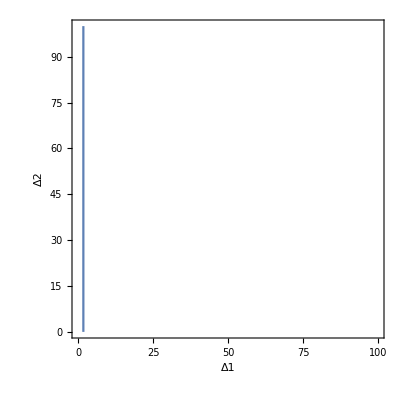

```mathematica
ContourPlot[S==Sc,{Δ1,0,100},{Δ2,0,100},AxesLabel->Automatic]
```

```mathematica
Plot3D[{T,Tc},{Δ1,0,100},{Δ2,0,100},AxesLabel->Automatic]
```

-Graphics3D-

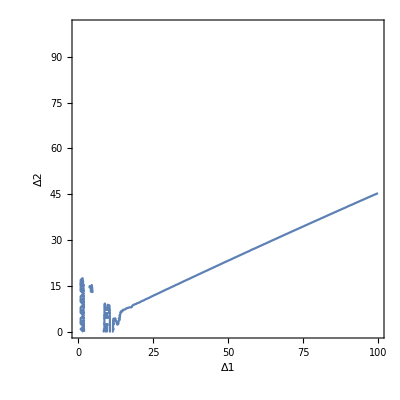

```mathematica
ContourPlot[T==Tc,{Δ1,0,100},{Δ2,0,100},AxesLabel->Automatic]
```

```mathematica
Plot3D[{U,Uc},{Δ1,0,100},{Δ2,0,100},AxesLabel->Automatic]
```

-Graphics3D-

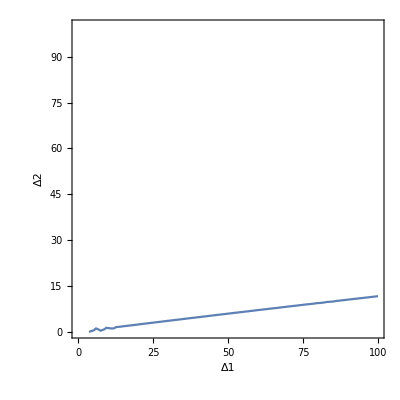

```mathematica
ContourPlot[U==Uc,{Δ1,0,100},{Δ2,0,100},AxesLabel->Automatic]
```

```mathematica
Plot[S/.Δ2->0,{Δ1,0,100}]
```

-Graphics-